```mathematica
Flatten[Map[ConstantArray[#[[1]],#[[2]]]&,FactorInteger[1324]]]
```

{2,2,331}

```mathematica
minfaca[x_]:=Min[Map[x/Apply[Times,#]+Apply[Times,#]&,Block[{list=Flatten[Map[ConstantArray[#[[1]],#[[2]]]&,FactorInteger[x]]]},Block[{L=Length[list]},

Table[Table[
list[[i]]^(PadLeft[IntegerDigits[j,2],L][[i]])
,{i,1,L}],{j,1,2^L-1}]]]]]
minfac[x_]:=Piecewise[{{minfaca[x], PrimeQ[x]==False}, {x, PrimeQ[x]==True}}]
```

```mathematica
minfac[1324]
```

335

```mathematica
Map[minfac,Range[1000]]
```

{2,2,3,4,5,5,7,6,6,7,11,7,13,9,8,8,17,9,19,9,10,13,23,10,10,15,12,11,29,11,31,12,14,19,12,12,37,21,16,13,41,13,43,15,14,25,47,14,14,15,20,17,53,15,16,15,22,31,59,16,61,33,16,16,18,17,67,21,26,17,71,17,73,39,20,23,18,19,79,18,18,43,83,19,22,45,32,19,89,19,20,27,34,49,24,20,97,21,20,20,101,23,103,21,22,55,107,21,109,21,40,22,113,25,28,33,22,61,24,22,22,63,44,35,30,23,127,24,46,23,131,23,26,69,24,25,137,29,139,24,50,73,24,24,34,75,28,41,149,25,151,27,26,25,36,25,157,81,56,26,30,27,163,45,26,85,167,26,26,27,28,47,173,35,32,27,62,91,179,27,181,27,64,31,42,37,28,51,30,29,191,28,193,99,28,28,197,29,199,30,70,103,36,29,46,105,32,29,30,29,211,57,74,109,48,30,38,111,76,31,30,43,223,30,30,115,227,31,229,33,32,37,233,31,52,63,82,31,239,31,241,33,36,65,42,47,32,39,86,35,251,32,34,129,32,32,257,49,44,33,38,133,263,34,58,33,92,71,269,33,271,33,34,139,36,35,277,141,40,34,281,53,283,75,34,35,48,34,34,39,100,77,293,35,64,45,38,151,36,35,50,153,104,35,66,35,307,36,106,41,311,37,313,159,36,83,317,59,40,36,110,37,36,36,38,165,112,49,54,37,331,87,46,169,72,37,337,39,116,37,42,37,56,51,38,175,347,41,349,39,40,38,353,65,76,93,38,181,359,38,38,183,44,40,78,67,367,39,50,47,60,43,373,39,40,55,42,39,379,39,130,193,383,40,46,195,52,101,389,41,40,42,134,199,84,40,397,201,40,40,401,73,44,105,42,43,48,41,409,51,140,107,66,41,88,42,142,41,419,41,421,213,56,61,42,77,68,111,46,53,431,42,433,45,44,113,42,79,439,42,42,43,443,49,94,225,152,44,449,43,52,117,154,229,48,43,457,231,44,43,461,43,463,45,46,235,467,44,74,57,160,67,54,85,44,45,62,241,479,44,50,243,44,44,102,45,487,69,166,49,491,53,46,45,48,47,78,89,499,45,170,253,503,45,106,45,52,131,509,47,80,48,46,259,108,55,58,51,176,46,521,47,523,135,46,265,48,46,46,63,68,47,54,95,112,75,182,271,60,47,541,273,184,49,114,47,547,141,70,47,48,47,86,279,52,143,557,49,56,48,50,283,563,59,118,285,48,79,569,49,571,48,194,55,48,48,577,51,196,49,90,103,64,81,54,295,587,49,50,69,200,53,593,49,52,153,202,49,599,49,601,57,76,155,66,107,607,51,50,71,60,52,613,309,56,50,617,109,619,51,50,313,96,50,50,315,52,161,54,51,631,87,214,319,132,65,62,51,80,52,641,113,643,51,58,53,647,51,70,51,52,167,653,115,136,57,82,61,659,52,661,333,56,91,54,55,52,171,226,77,72,52,673,339,52,52,677,119,104,54,230,53,683,55,142,63,232,59,66,53,691,177,54,349,144,53,58,351,236,53,701,53,56,54,62,355,108,71,709,81,88,97,54,55,68,183,242,361,719,54,110,57,244,185,54,55,727,54,54,83,60,73,733,369,56,55,78,59,739,57,58,67,743,55,154,375,92,56,114,55,751,63,254,55,156,55,757,381,56,58,761,133,116,195,62,385,72,56,769,57,260,197,773,61,56,105,58,391,60,56,82,57,56,56,162,137,787,201,266,89,120,57,74,399,68,203,797,59,64,57,98,403,84,79,58,57,272,109,809,57,811,57,274,59,168,58,62,411,60,61,821,143,823,111,58,73,827,59,829,93,280,58,66,145,172,60,58,421,839,58,58,423,284,215,78,65,88,69,286,59,60,83,853,75,64,115,857,59,859,63,62,433,863,59,178,435,68,59,90,59,80,117,106,61,60,85,877,441,296,62,881,63,883,60,74,445,887,61,134,99,60,227,66,155,184,60,62,451,60,60,70,63,64,121,186,157,907,231,110,61,911,62,94,459,76,233,138,61,919,63,310,463,84,61,62,465,112,61,929,61,68,237,314,469,72,62,937,81,316,67,941,163,64,75,62,65,947,91,86,63,320,62,953,71,196,243,62,481,144,62,62,63,116,245,198,65,967,66,70,107,971,63,146,489,64,77,977,169,100,63,118,493,983,65,202,63,68,64,66,63,991,63,334,85,204,95,997,501,64,65}

```mathematica
Map[minfac,%]
```

{2,2,3,4,5,5,7,5,5,7,11,7,13,5,5,5,17,5,19,5,7,13,23,7,7,5,7,11,29,11,31,7,5,19,7,7,37,7,5,13,41,13,43,5,5,7,47,5,5,5,5,17,53,5,5,5,13,31,59,5,61,5,5,5,5,17,67,7,5,17,71,17,73,5,5,23,5,19,79,5,5,43,83,19,13,5,7,19,89,19,5,7,19,5,7,5,97,7,5,5,101,23,103,7,13,5,107,7,109,7,13,13,113,7,11,5,13,61,7,13,13,5,5,7,11,23,127,7,7,23,131,23,5,5,7,7,137,29,139,7,5,73,7,7,19,5,11,41,149,7,151,7,5,7,7,7,157,5,5,5,11,7,163,5,5,13,167,5,5,7,11,47,173,7,7,7,5,5,179,7,181,7,5,31,13,37,11,5,11,29,191,11,193,5,11,11,197,29,199,11,17,103,7,29,7,13,7,29,11,29,211,13,5,109,5,11,7,13,23,31,11,43,223,11,11,11,227,31,229,5,7,37,233,31,17,5,43,31,239,31,241,5,7,5,13,47,7,5,5,7,251,7,19,7,7,7,257,5,5,5,7,5,263,19,31,5,7,71,269,5,271,5,19,139,7,7,277,5,13,19,281,53,283,5,19,7,5,19,19,5,5,5,293,7,5,5,7,151,7,7,5,5,7,7,17,7,307,7,5,41,311,37,313,5,7,83,317,59,13,7,7,37,7,7,7,5,13,5,5,37,331,7,7,5,17,37,337,5,5,37,13,37,5,5,7,7,347,41,349,5,13,7,353,5,23,19,7,181,359,7,7,5,5,13,19,67,367,5,5,47,5,43,373,5,13,5,13,5,379,5,23,193,383,13,7,11,17,101,389,41,13,13,5,199,19,13,397,17,13,13,401,73,5,13,13,43,5,41,409,5,7,107,17,41,19,13,73,41,419,41,421,5,5,61,13,5,7,13,7,53,431,13,433,5,5,113,13,79,439,13,13,43,443,5,5,11,7,5,449,43,17,13,7,229,5,43,457,7,5,43,461,43,463,5,7,17,467,5,5,13,5,67,5,13,5,5,5,241,479,5,5,7,5,5,23,5,487,5,13,5,491,53,7,5,5,47,19,89,499,5,7,19,503,5,5,5,17,131,509,47,5,5,7,5,7,5,31,5,7,7,521,47,523,7,7,31,5,7,7,5,7,47,5,7,13,5,7,271,5,47,541,19,31,5,7,47,547,5,17,47,5,47,5,13,17,7,557,5,5,5,5,283,563,59,61,19,5,79,569,5,571,5,5,5,5,5,577,5,11,5,19,103,5,5,5,5,587,5,5,5,11,53,593,5,17,5,103,5,599,5,601,13,23,7,17,107,607,5,5,71,5,17,613,5,5,5,617,109,619,5,5,313,5,5,5,7,17,11,5,5,631,7,109,13,23,5,5,5,5,17,641,113,643,5,31,53,647,5,17,5,17,167,653,11,7,13,43,61,659,17,661,7,5,5,5,5,17,11,11,5,17,17,673,5,17,17,677,7,7,5,5,53,683,5,73,5,37,59,17,53,691,5,5,349,7,53,31,13,5,53,701,53,5,5,5,23,7,71,709,5,19,97,5,5,7,5,5,7,719,5,7,13,5,13,5,5,727,5,5,83,5,73,733,5,5,5,19,59,739,13,31,67,743,5,7,13,7,5,7,5,751,5,7,5,7,5,757,23,5,31,761,5,5,11,5,7,17,5,769,13,5,197,773,61,5,13,31,13,5,5,43,13,5,5,7,137,787,17,5,89,13,13,5,13,7,7,797,59,5,13,7,5,19,79,31,13,5,109,809,13,811,13,139,59,5,31,5,7,5,61,821,7,823,13,31,73,827,59,829,19,19,31,17,19,47,5,31,421,839,31,31,5,5,5,19,5,19,5,7,59,5,83,853,5,5,11,857,59,859,5,5,433,863,59,5,5,7,59,19,59,5,13,5,61,5,13,877,13,5,5,881,5,883,5,5,5,887,61,5,5,5,227,17,7,31,5,5,17,5,5,17,5,5,13,37,157,907,7,7,61,911,5,5,5,23,233,29,61,919,5,41,463,19,61,5,7,13,61,929,61,7,43,5,5,17,5,937,5,83,67,941,163,5,5,5,5,947,5,5,5,7,5,953,71,11,7,5,5,7,5,5,5,5,13,29,5,967,17,17,107,971,5,5,13,5,5,977,5,5,5,61,7,983,5,103,5,7,5,17,5,991,5,5,13,29,7,997,7,5,5}

```mathematica
mford[x_]:=Block[{c=0,n=x,m=minfac[x]},
While[n≠m,n=m;m=minfac[m];c++];{c,m}]
```

```mathematica
Monitor[Table[mford[k],{k,1,100000}],{k,i}]
```

{{1,2},{0,2},{0,3},{0,4},{0,5},{1,5},{0,7},{2,5},{2,5},{1,7},{0,11},{1,7},{0,13},{3,5},{3,5},{3,5},{0,17},{3,5},{0,19},{3,5},{2,7},{1,13},{0,23},«99954»,{1,991},{2,61},{7,5},{2,53},{1,49993},{2,179},{1,2131},{2,283},{7,5},{7,5},{4,13},{0,99989},{3,109},{0,99991},{6,5},{8,5},{3,23},{4,19},{1,797},{6,5},{7,13},{3,17},{6,5}}

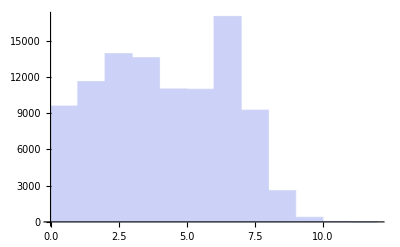

```mathematica
Histogram[Map[First,Out[331]]]
```

```mathematica
Table[{First[Out[331][[i]]],i},{i,1,100000}]
```

{{1,1},{0,2},{0,3},{0,4},{0,5},{1,6},{0,7},{2,8},{2,9},{1,10},{0,11},{1,12},{0,13},{3,14},{3,15},{3,16},{0,17},{3,18},{0,19},«99962»,{1,99982},{2,99983},{1,99984},{2,99985},{7,99986},{7,99987},{4,99988},{0,99989},{3,99990},{0,99991},{6,99992},{8,99993},{3,99994},{4,99995},{1,99996},{6,99997},{7,99998},{3,99999},{6,100000}}

```mathematica
Select[Out[335],First[#]==1&]
```

{{1,1},{1,6},{1,10},{1,12},{1,22},{1,28},{1,30},{1,34},{1,40},{1,42},{1,52},{1,58},{1,66},{1,70},{1,72},{1,76},{1,78},{1,82},«11582»,{1,99838},{1,99858},{1,99862},{1,99868},{1,99870},{1,99874},{1,99888},{1,99906},{1,99910},{1,99930},{1,99940},{1,99952},{1,99958},{1,99964},{1,99978},{1,99982},{1,99984},{1,99996}}

```mathematica
Sort[Out[331],First[#1]>First[#2]&]
```

{{11,5},{11,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{10,5},{9,5},{9,5},{9,5},{9,5},{9,5},{9,5},{9,5},{9,5},{9,5},{9,5},{9,5},{9,5},{9,5},{9,5},{9,5},«99888»,{0,257},{0,251},{0,241},{0,239},{0,233},{0,229},{0,227},{0,223},{0,211},{0,199},{0,197},{0,193},{0,191},{0,181},{0,179},{0,173},{0,167},{0,163},{0,157},{0,151},{0,149},{0,139},{0,137},{0,131},{0,127},{0,113},{0,109},{0,107},{0,103},{0,101},{0,97},{0,89},{0,83},{0,79},{0,73},{0,71},{0,67},{0,61},{0,59},{0,53},{0,47},{0,43},{0,41},{0,37},{0,31},{0,29},{0,23},{0,19},{0,17},{0,13},{0,11},{0,7},{0,5},{0,4},{0,3},{0,2}}

```mathematica
Position[Out[331],{11,5}]
```

{{27933},{55694}}

```mathematica
minfac[27933]
```

```mathematica
minfac[9314]
```

```mathematica
minfac[4659]
```

```mathematica
minfac[1556]
```

```mathematica
minfac[393]
```

```mathematica
minfac[134]
```

```mathematica
minfac[69]
```

```mathematica
minfac[26]
```

```mathematica
minfac[15]
```

```mathematica
minfac[8]
```

```mathematica
minfac[6]
```

5

```mathematica
Map[FactorInteger,{{27933},{55694}}]
```

{{{{3,1},{9311,1}}},{{{2,1},{27847,1}}}}

```mathematica
Map[DivisorSigma[0,#[[2]]]&,Out[339]]
```

{1,4,4,6,4,6,8,4,8,8,6,4,8,8,12,6,8,4,12,8,12,8,4,12,8,12,8,4,6,6,8,8,8,12,4,12,10,16,4,12,8,12,8,12,8,20,8,6,4,8,4,8,16,6,8,8,16,20,12,12,12,4,8,«11493»,8,40,32,16,24,72,12,30,4,48,32,32,28,64,16,8,72,8,4,32,24,24,8,12,16,18,32,8,32,16,6,16,18,24,8,12,16,12,24,16,12,12,16,8,4,32,12,6,16,4,20,8,16,16,24,10,16,12,16,4,20,24}

```mathematica
Table[First[Out[331][[i]]],{i,1,100000}]
```

{1,0,0,0,0,1,0,2,2,1,0,1,0,3,3,3,0,3,0,3,2,1,0,2,2,4,2,1,0,1,0,2,4,1,2,2,0,3,4,1,0,1,0,4,4,3,0,4,4,4,4,1,0,4,4,4,2,1,0,4,0,5,4,4,4,1,0,3,5,1,0,1,0,5,4,1,4,1,0,«99842»,3,0,8,4,5,8,3,0,1,8,3,8,5,6,3,4,7,7,1,2,7,5,3,4,5,2,6,7,7,3,1,5,6,2,9,6,1,7,4,0,3,6,1,5,3,3,6,2,6,0,3,2,3,6,7,4,1,2,7,2,1,2,1,2,7,7,4,0,3,0,6,8,3,4,1,6,7,3,6}

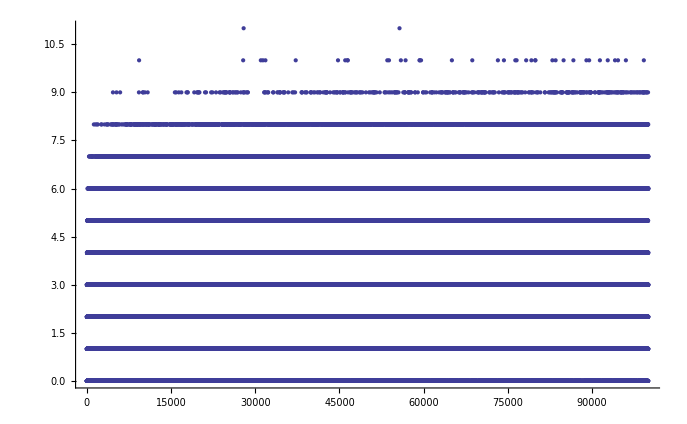

```mathematica
ListPlot[%]
```

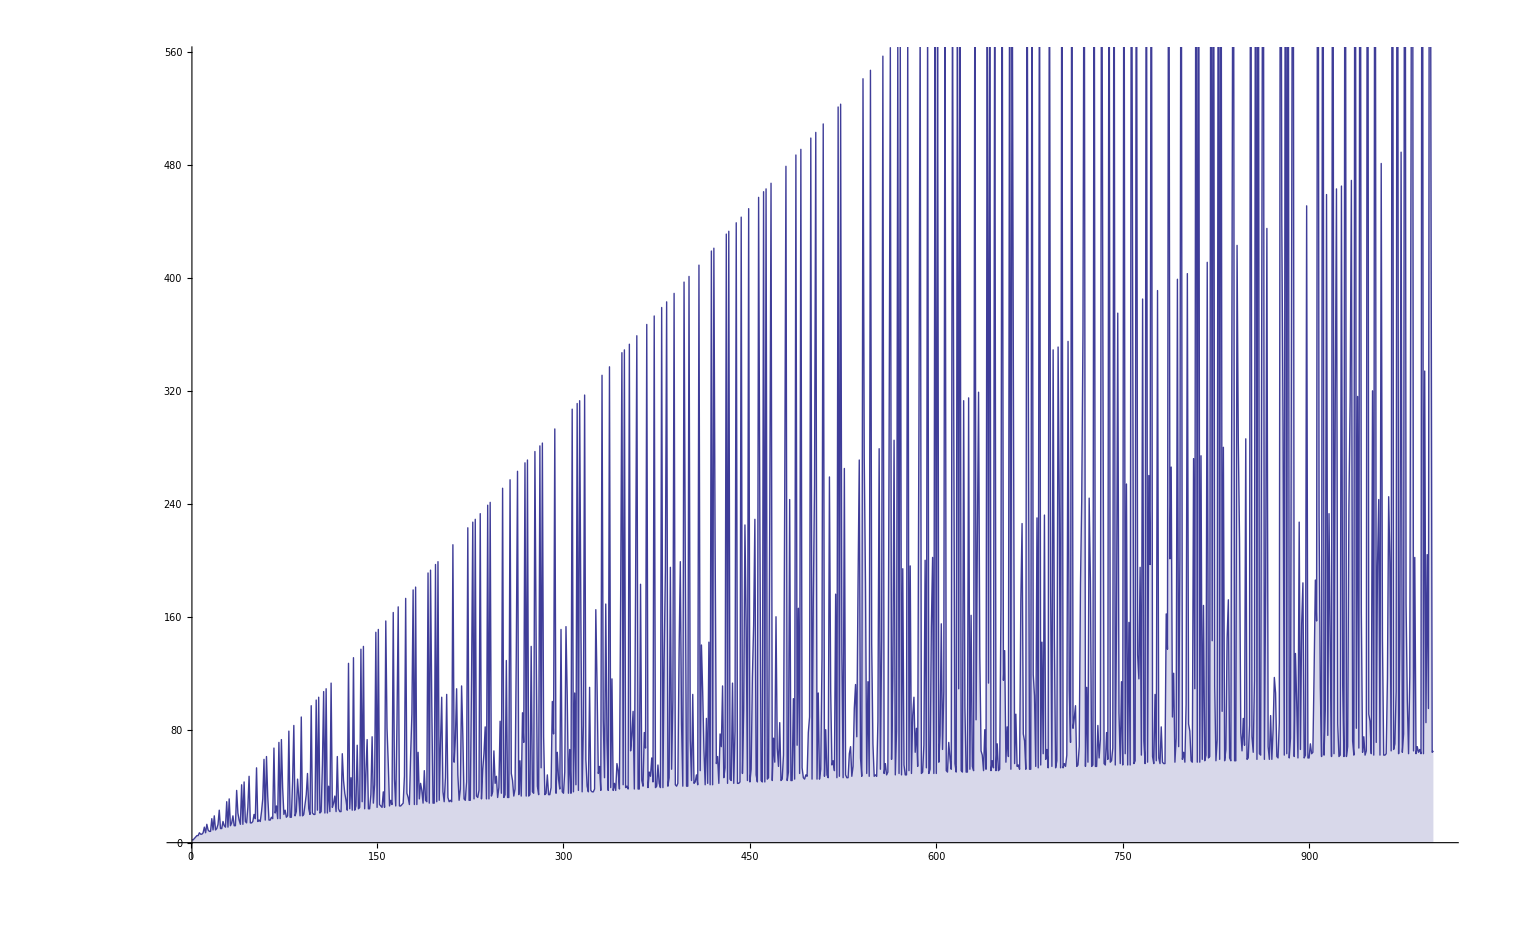

```mathematica
DiscretePlot[minfac[k],{k,1,1000}]
```

```mathematica
∏_(i=1)^20 Prime[i]
```

```mathematica
minfac[557940830126698960967415390]
```

```mathematica
minfac[47241542381273]
```

47241542381273

```mathematica
minfac[6469693230]
```

```mathematica
minfac[160879]
```

160879

```mathematica
mford[55794083012669896096741539]
```

{4,4217}

```mathematica
10000000/160220.88
```

62.4138

```mathematica
minfac[17!]
```

$Aborted

```mathematica
Monitor[Table[mford[d!],{d,1,17}],{d,c,n,m}]
```

$Aborted

```mathematica
10000000/170538.6
```

```mathematica
Table[minfac[∏_(i=1)^j Prime[i]],{j,1,20}]
```

{2,5,11,29,97,347,1429,6229,29873,160879,895681,5448239,34885673,228759799,1568299433,11417382973,87698582693,684947829299,5606539600699,47241542381273}

```mathematica
minfac[∏_(i=1)^21 Prime[i]]
```

```mathematica
PrimeQ[403631914511993]
```

False

```mathematica
Map[PrimeQ,%]
```

{True,True,True,True,True,True,True,True,True,True,True,False,True,False,True,False,False,False,False,True}

```mathematica
Position[%,False]
```

{{12},{14},{16},{17},{18},{19}}

```mathematica
Table[x(x+1),{x,1,10}]
```

{2,6,12,20,30,42,56,72,90,110}

```mathematica
∑_(i=2)^∞ 1/i^2
```

-1+π^2/6

```mathematica
∑_(i=2)^∞ 1/(i^2+i)
```

1/2

```mathematica
Timing[Total[Monitor[Table[Block[{d=Abs[Det[Partition[Permute[Range[16],RandomPermutation[16]],4]]]},Piecewise[{{1, d<2}, {0, d>1}}]],{i,1,1000000}],i]]]
```

{55.4359,531}

```mathematica
531/1000000
```

```mathematica
400000000*531/1000000//N
```

212400.

```mathematica
16!*531/1000000//N
```

1.111×10^10

```mathematica
x[[1]]
```

```mathematica
CharacteristicPolynomial[{{12,16,14,15},{13,7,8,10},{2,11,5,1},{3,4,6,9}},y]
```

-1+79 y-20 y^2-33 y^3+y^4

```mathematica
Map[CharacteristicPolynomial[#,y]&,x]
```

{-1+79 y-20 y^2-33 y^3+y^4,1-1958 y+18 y^2-32 y^3+y^4,-1-465 y+145 y^2-37 y^3+y^4,1-563 y-203 y^2-28 y^3+y^4,-1-1476 y+129 y^2-38 y^3+y^4,-1+511 y+110 y^2-37 y^3+y^4,1-444 y+44 y^2-36 y^3+y^4,-1-453 y-226 y^2-25 y^3+y^4,-1-2126 y-451 y^2-18 y^3+y^4,-1+1085 y-136 y^2-31 y^3+y^4,-1-1426 y+354 y^2-44 y^3+y^4,1+23 y+88 y^2-35 y^3+y^4,1+1117 y-191 y^2-28 y^3+y^4,-1-1073 y+192 y^2-39 y^3+y^4,1-1216 y-14 y^2-32 y^3+y^4,1-1149 y+485 y^2-46 y^3+y^4,«19312»,1+323 y+76 y^2-38 y^3+y^4,1+1100 y+99 y^2-36 y^3+y^4,-1+1092 y+202 y^2-40 y^3+y^4,1+505 y-124 y^2-31 y^3+y^4,1-672 y-211 y^2-25 y^3+y^4,1+1393 y-65 y^2-33 y^3+y^4,-1+990 y-47 y^2-33 y^3+y^4,-1-2218 y+56 y^2-34 y^3+y^4,1-2420 y+450 y^2-45 y^3+y^4,1-626 y-96 y^2-32 y^3+y^4,-1+311 y-42 y^2-34 y^3+y^4,1+307 y-29 y^2-34 y^3+y^4,1+1741 y+169 y^2-40 y^3+y^4,1-814 y-57 y^2-33 y^3+y^4,1+2683 y-152 y^2-30 y^3+y^4,1+270 y-226 y^2-28 y^3+y^4}

```mathematica
Select[x,IrreduciblePolynomialQ[Factor[CharacteristicPolynomial[#,y]]]==False&]
```

{{{3,1,6,4},{10,7,12,8},{9,11,2,5},{16,15,13,14}},{{16,9,8,10},{6,3,1,5},{4,12,15,2},{11,13,14,7}},{{13,14,8,6},{7,9,1,15},{4,5,11,10},{2,3,16,12}},{{16,2,6,7},{10,9,4,5},{13,8,1,12},{14,15,3,11}},{{16,1,13,11},{10,5,9,14},{2,15,8,6},{3,7,4,12}},{{3,11,10,6},{4,15,14,9},{2,7,5,1},{8,12,16,13}},{{10,12,11,16},{2,6,9,7},{8,13,14,15},{1,4,5,3}},{{4,15,6,16},{9,10,7,3},{11,14,13,8},{5,2,12,1}},{{7,5,16,1},{11,14,15,2},{10,9,13,8},{6,3,4,12}},{{11,8,7,4},{15,5,16,9},{14,1,12,3},{2,6,10,13}},{{13,9,1,2},{14,12,15,6},{16,11,5,3},{4,10,8,7}},{{6,16,2,3},{10,14,11,4},{5,12,1,13},{9,15,8,7}},{{13,16,6,14},{9,15,5,7},{8,12,11,3},{4,10,1,2}},{{5,2,7,8},{16,1,9,6},{13,3,11,10},{12,4,14,15}},{{9,3,5,10},{1,8,11,7},{15,2,4,14},{6,12,16,13}},{{8,9,12,4},{7,14,16,2},{3,1,5,13},{10,11,15,6}},{{3,11,8,13},{5,6,4,7},{1,9,12,10},{2,14,15,16}},{{9,16,10,12},{4,5,15,6},{2,1,11,3},{14,8,7,13}},{{5,6,9,1},{10,2,14,3},{8,11,4,12},{16,7,15,13}},{{7,1,6,11},{15,5,13,10},{12,2,9,16},{14,3,4,8}},{{15,12,1,14},{16,2,10,11},{13,3,8,9},{7,6,4,5}},{{12,8,9,14},{5,7,1,10},{2,3,16,4},{15,6,11,13}},{{9,11,4,7},{8,12,1,5},{10,14,3,6},{13,16,2,15}},{{15,12,10,16},{11,4,1,7},{8,9,5,13},{2,6,14,3}},{{15,12,10,14},{6,7,9,11},{2,5,16,8},{1,3,13,4}},{{5,7,6,2},{14,9,10,8},{1,16,12,13},{3,15,11,4}},{{13,12,3,15},{8,10,9,2},{6,14,16,11},{1,5,7,4}},{{13,14,16,7},{11,10,12,6},{1,4,5,2},{15,9,8,3}},{{10,11,16,1},{7,15,8,4},{6,13,5,3},{9,12,14,2}},{{5,16,2,11},{4,8,3,6},{15,10,13,14},{7,9,1,12}},{{7,6,11,13},{3,16,1,8},{5,2,10,4},{9,15,14,12}},{{3,14,11,9},{6,16,5,13},{8,1,7,12},{10,4,2,15}},{{16,2,7,1},{15,14,3,9},{12,6,5,4},{11,13,8,10}},{{9,16,14,10},{3,8,5,2},{1,7,4,12},{6,15,11,13}},{{8,15,1,16},{3,11,14,5},{4,12,10,7},{6,9,2,13}},{{3,1,4,2},{7,8,12,9},{5,14,13,15},{11,6,16,10}},{{3,2,10,14},{7,12,13,6},{5,1,11,4},{8,16,15,9}},{{16,14,11,6},{1,7,15,8},{12,9,5,10},{4,3,2,13}},{{6,2,8,5},{13,16,9,11},{4,7,1,3},{14,10,15,12}},{{12,4,13,2},{11,8,15,3},{1,9,5,6},{7,16,14,10}},{{10,1,9,7},{3,11,13,12},{14,4,5,16},{6,8,2,15}},{{12,15,9,16},{8,1,4,14},{2,5,7,13},{11,10,3,6}},{{8,2,3,14},{5,6,4,15},{13,1,9,12},{7,10,11,16}},{{7,12,1,6},{9,2,4,8},{16,5,10,14},{13,3,15,11}},{{6,14,10,9},{5,7,4,3},{2,13,11,16},{12,15,8,1}},{{3,8,16,10},{12,4,13,11},{2,5,7,6},{14,9,1,15}},{{7,5,4,6},{1,3,15,9},{13,12,2,14},{16,10,8,11}},{{5,16,9,12},{8,14,11,7},{2,1,15,13},{3,10,4,6}},{{5,4,12,16},{13,15,2,11},{3,1,7,10},{6,14,8,9}},{{7,15,6,12},{14,8,1,3},{2,10,4,9},{13,16,5,11}},{{12,8,5,4},{1,3,13,16},{6,9,2,15},{14,11,7,10}},{{13,16,15,12},{11,7,1,6},{4,10,2,9},{3,8,14,5}},{{2,13,6,12},{5,15,10,9},{3,11,7,14},{1,8,4,16}},{{11,8,15,2},{9,1,12,5},{7,14,16,6},{10,4,13,3}},{{14,11,9,15},{5,3,16,10},{6,4,12,13},{2,1,8,7}},{{5,4,3,6},{13,16,15,11},{14,1,2,10},{12,8,9,7}},{{5,11,15,12},{6,8,3,1},{2,9,16,14},{4,7,13,10}},{{2,7,6,4},{10,16,12,9},{13,8,15,1},{3,11,14,5}},{{12,3,1,15},{13,9,2,14},{10,7,16,11},{6,8,4,5}},{{10,5,7,9},{2,13,1,8},{15,16,12,4},{14,6,11,3}},{{11,14,13,5},{7,6,4,10},{8,16,15,12},{1,3,2,9}},{{2,14,10,13},{7,1,4,11},{8,3,5,9},{6,15,12,16}},{{7,14,12,16},{15,11,3,5},{9,10,8,13},{6,4,1,2}},{{2,4,9,6},{16,15,11,7},{13,1,5,14},{8,12,10,3}},{{13,7,8,1},{2,15,12,3},{14,6,5,4},{11,16,10,9}},{{14,11,16,8},{4,9,3,6},{10,7,15,13},{5,12,1,2}},{{4,10,11,16},{6,7,13,15},{3,1,9,8},{2,5,12,14}},{{7,14,11,15},{2,3,9,4},{5,16,10,13},{1,12,8,6}},{{10,12,1,6},{4,15,13,14},{7,16,3,8},{5,2,11,9}},{{10,6,1,5},{7,2,13,11},{12,9,15,8},{14,3,4,16}},{{9,5,16,3},{12,10,13,2},{7,6,11,1},{15,4,14,8}},{{6,13,8,10},{14,12,3,15},{2,7,4,5},{1,16,11,9}},{{6,14,11,8},{1,10,15,4},{7,16,13,9},{12,5,3,2}},{{15,5,14,7},{12,16,6,9},{8,13,2,3},{4,11,1,10}},{{12,11,3,14},{16,13,15,9},{1,5,6,2},{4,10,7,8}},{{13,8,6,3},{16,12,10,9},{11,2,1,7},{15,5,4,14}},{{5,15,16,3},{7,12,4,9},{14,11,13,6},{10,2,8,1}},{{13,8,6,16},{15,14,5,3},{7,9,2,10},{12,11,4,1}},{{7,3,10,1},{6,14,9,15},{2,11,4,13},{12,8,16,5}},{{15,10,14,9},{2,1,13,11},{6,4,7,3},{12,8,16,5}},{{1,11,9,2},{6,13,16,4},{5,12,14,8},{7,10,15,3}},{{11,16,10,8},{13,6,1,4},{2,12,7,3},{9,5,14,15}},{{1,8,16,4},{7,9,13,14},{5,11,12,10},{2,15,6,3}},{{10,15,11,13},{2,12,8,7},{14,6,3,16},{5,4,1,9}},{{15,10,14,16},{2,6,8,9},{13,3,11,12},{1,7,4,5}},{{4,6,7,1},{12,14,13,2},{5,9,11,3},{8,15,16,10}},{{5,13,9,10},{6,8,15,2},{3,16,7,14},{1,12,4,11}},{{9,14,7,12},{1,15,8,11},{3,6,10,13},{4,16,2,5}},{{4,16,10,15},{7,3,14,9},{8,13,5,6},{1,2,12,11}},{{8,5,9,11},{13,1,2,10},{6,7,16,14},{4,3,15,12}},{{14,16,10,9},{8,3,11,1},{6,13,2,7},{5,15,12,4}},{{5,15,1,4},{9,14,11,12},{7,2,10,16},{6,3,8,13}},{{13,14,8,12},{15,16,10,11},{7,4,9,1},{5,3,6,2}}}

```mathematica
Map[Det,Out[515]]
```

{1,-1,1,-1,-1,-1,-1,1,-1,1,-1,-1,1,1,-1,1,1,1,1,-1,1,-1,1,-1,1,-1,-1,1,-1,-1,1,-1,-1,1,1,-1,-1,1,-1,-1,-1,-1,1,-1,1,-1,1,-1,1,-1,-1,-1,1,1,-1,1,1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,-1,1,1,-1,1,1,-1,-1,1,1,-1,1,1,1,1,1,1,1,-1,1,-1,-1,-1,1,-1,-1}

```mathematica
Table[{j,Factor[CharacteristicPolynomial[Out[515][[j]],y]]},{j,1,93}]//Column
```

{1,(-1+y) (-1-261 y-25 y^2+y^3)}
{2,(-1+y) (1+230 y-40 y^2+y^3)}
{3,(-1+y) (-1+359 y-44 y^2+y^3)}
{4,(-1+y) (1+80 y-36 y^2+y^3)}
{5,(-1+y) (1+230 y-40 y^2+y^3)}
{6,(-1+y) (1+65 y-35 y^2+y^3)}
{7,(1+y) (-1+60 y-34 y^2+y^3)}
{8,(-1+y) (-1-259 y-27 y^2+y^3)}
{9,(-1+y) (1+340 y-45 y^2+y^3)}
{10,(-1+y) (-1+245 y-40 y^2+y^3)}
{11,(1+y) (-1+130 y-38 y^2+y^3)}
{12,(-1+y) (1-269 y-27 y^2+y^3)}
{13,(1+y) (1+242 y-42 y^2+y^3)}
{14,(1+y) (1-51 y-33 y^2+y^3)}
{15,(1+y) (-1-20 y-35 y^2+y^3)}
{16,(-1+y) (-1-20 y-32 y^2+y^3)}
{17,(1+y) (1+127 y-38 y^2+y^3)}
{18,(-1+y) (-1+151 y-37 y^2+y^3)}
{19,(-1+y) (-1-345 y-23 y^2+y^3)}
{20,(1+y) (-1-20 y-30 y^2+y^3)}
{21,(1+y) (1-113 y-31 y^2+y^3)}
{22,(-1+y) (1+421 y-47 y^2+y^3)}
{23,(-1+y) (-1+168 y-38 y^2+y^3)}
{24,(-1+y) (1-276 y-26 y^2+y^3)}
{25,(1+y) (1+364 y-43 y^2+y^3)}
{26,(-1+y) (1-245 y-29 y^2+y^3)}
{27,(-1+y) (1+270 y-42 y^2+y^3)}
{28,(1+y)^2 (1-33 y+y^2)}
{29,(-1+y) (1-72 y-31 y^2+y^3)}
{30,(-1+y) (1+215 y-37 y^2+y^3)}
{31,(1+y) (1+416 y-46 y^2+y^3)}
{32,(1+y) (-1+270 y-42 y^2+y^3)}
{33,(-1+y) (1+388 y-44 y^2+y^3)}
{34,(-1+y) (-1+61 y-33 y^2+y^3)}
{35,(1+y) (1+326 y-43 y^2+y^3)}
{36,(-1+y) (1-137 y-33 y^2+y^3)}
{37,(-1+y) (1+56 y-34 y^2+y^3)}
{38,(1+y) (1+284 y-42 y^2+y^3)}
{39,(-1+y) (1+14 y-34 y^2+y^3)}
{40,(-1+y) (1+74 y-34 y^2+y^3)}
{41,(1+y) (-1+296 y-42 y^2+y^3)}
{42,(1+y) (-1-263 y-27 y^2+y^3)}
{43,(-1+y) (-1+71 y-38 y^2+y^3)}
{44,(-1+y) (1-172 y-29 y^2+y^3)}
{45,(1+y) (1-188 y-26 y^2+y^3)}
{46,(1+y) (-1-137 y-30 y^2+y^3)}
{47,(1+y) (1-338 y-24 y^2+y^3)}
{48,(-1+y) (1+205 y-39 y^2+y^3)}
{49,(-1+y) (-1+3 y-35 y^2+y^3)}
{50,(1+y) (-1-125 y-31 y^2+y^3)}
{51,(1+y) (-1-228 y-28 y^2+y^3)}
{52,(1+y) (-1-187 y-28 y^2+y^3)}
{53,(1+y) (1+241 y-41 y^2+y^3)}
{54,(1+y) (1-144 y-32 y^2+y^3)}
{55,(1+y) (-1+169 y-37 y^2+y^3)}
{56,(1+y) (1-45 y-31 y^2+y^3)}
{57,(1+y) (1+218 y-40 y^2+y^3)}
{58,(-1+y) (1+61 y-37 y^2+y^3)}
{59,(1+y) (-1+363 y-43 y^2+y^3)}
{60,(1+y) (1+201 y-39 y^2+y^3)}
{61,(-1+y) (1+244 y-40 y^2+y^3)}
{62,(1+y) (-1-371 y-25 y^2+y^3)}
{63,(-1+y) (-1-231 y-27 y^2+y^3)}
{64,(-1+y) (1-307 y-24 y^2+y^3)}
{65,(-1+y) (1+294 y-41 y^2+y^3)}
{66,(1+y) (-1+238 y-41 y^2+y^3)}
{67,(1+y) (-1+133 y-35 y^2+y^3)}
{68,(1+y) (-1-126 y-27 y^2+y^3)}
{69,(1+y) (1+106 y-38 y^2+y^3)}
{70,(1+y) (1+370 y-44 y^2+y^3)}
{71,(-1+y) (1+185 y-37 y^2+y^3)}
{72,(-1-36 y+y^2) (-1+5 y+y^2)}
{73,(-1+y) (-1-178 y-30 y^2+y^3)}
{74,(1+y) (-1+296 y-44 y^2+y^3)}
{75,(-1+y) (1+102 y-38 y^2+y^3)}
{76,(-1+y) (-1+174 y-39 y^2+y^3)}
{77,(1+y) (1-126 y-32 y^2+y^3)}
{78,(1+y) (-1-176 y-31 y^2+y^3)}
{79,(1+y) (1-139 y-31 y^2+y^3)}
{80,(1+y) (1-129 y-29 y^2+y^3)}
{81,(1+y) (1-152 y-32 y^2+y^3)}
{82,(1+y) (1+211 y-40 y^2+y^3)}
{83,(1+y) (1-336 y-26 y^2+y^3)}
{84,(1+y) (1+105 y-35 y^2+y^3)}
{85,(-1+y) (-1+92 y-36 y^2+y^3)}
{86,(-1+y) (1+196 y-38 y^2+y^3)}
{87,(-1+y) (-1-114 y-30 y^2+y^3)}
{88,(-1+y) (1+174 y-38 y^2+y^3)}
{89,(1+y) (-1-276 y-24 y^2+y^3)}
{90,(1+y) (-1+73 y-38 y^2+y^3)}
{91,(1+y) (1-299 y-24 y^2+y^3)}
{92,(-1+y) (1+244 y-41 y^2+y^3)}
{93,(-1+y) (1+101 y-39 y^2+y^3)}

```mathematica
Out[515][[28]]
```

```mathematica
MatrixForm[{{13,14,16,7},{11,10,12,6},{1,4,5,2},{15,9,8,3}}]
```

(13 | 14 | 16 | 7
11 | 10 | 12 | 6
1 | 4 | 5 | 2
15 | 9 | 8 | 3)

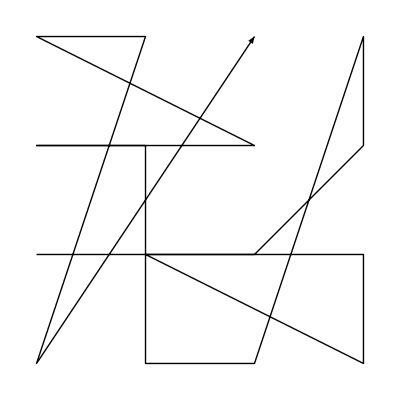
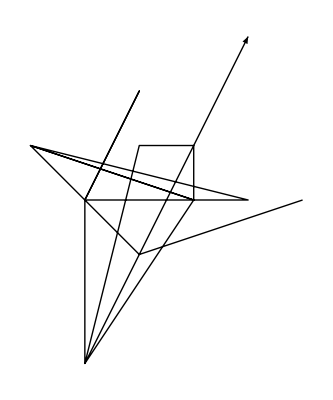
{(13 | 14 | 16 | 7
11 | 10 | 12 | 6
1 | 4 | 5 | 2
15 | 9 | 8 | 3),{-Graphics-,{{3,0},{0,-1},{-2,1},{1,0},{1,1},{0,1},{-1,-3},{-1,0},{0,2},{-1,0},{2,0},{-2,1},{1,0},{-1,-3},{2,3}},-Graphics-}}

```mathematica
GM[{{13,14,16,7},{11,10,12,6},{1,4,5,2},{15,9,8,3}}]
```

```mathematica
Factor[CharacteristicPolynomial[{{13,14,16,7},{11,10,12,6},{1,4,5,2},{15,9,8,3}},y]]
```

(1+y)^2 (1-33 y+y^2)

```mathematica
Table[{Prime[j],Factor[CharacteristicPolynomial[{{13,14,16,7},{11,10,12,6},{1,4,5,2},{15,9,8,3}},y],Modulus->Prime[j]]},{j,1,7}]//Column
```

{2,(1+y)^2 (1+y+y^2)}
{3,(1+y)^2 (1+y^2)}
{5,(1+y)^4}
{7,(1+y)^4}
{11,(1+y)^2 (1+y^2)}
{13,(1+y)^2 (1+6 y+y^2)}
{17,(1+y)^2 (1+y+y^2)}

```mathematica
Solve[CharacteristicPolynomial[{{13, 14, 16, 7}, {11, 10, 12, 6}, {1, 4, 5, 2}, {15, 9, 8, 3}}, y]==0,y]
```

{{y→-1},{y→-1},{y→2/(33+√1085)},{y→1/2 (33+√1085)}}

```mathematica
FindPermutation[Flatten[{{13,14,16,7},{11,10,12,6},{1,4,5,2},{15,9,8,3}}]]
```

```mathematica
Map[MatrixForm[Partition[Permute[Range[16],#],4]]&,GroupElements[PermutationGroup[{Cycles[{{1,9,14,2,12,7,4,10,6,8,15,13},{3,16},{5,11}}]}]]]
```

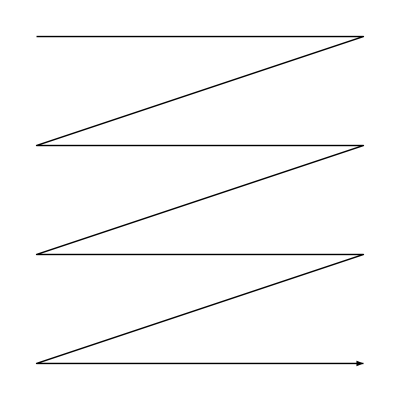
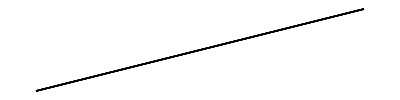
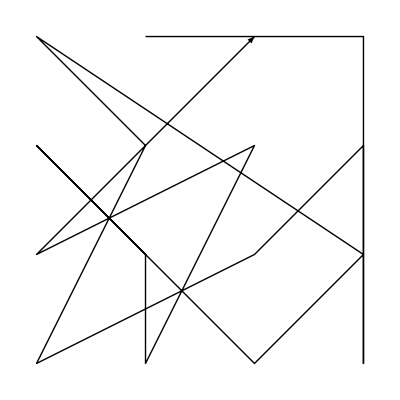
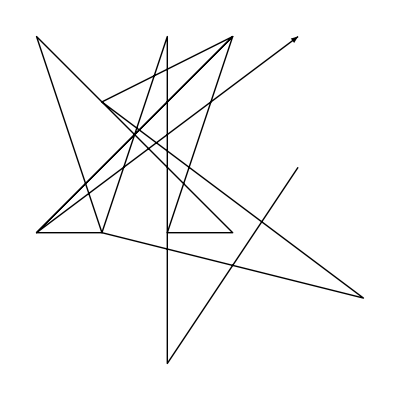
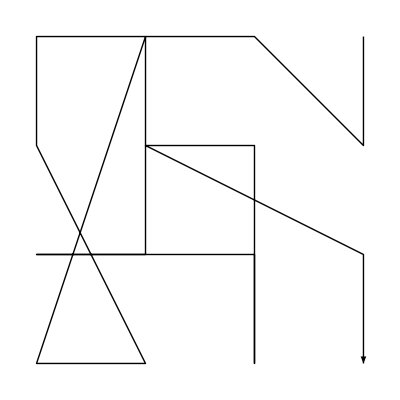
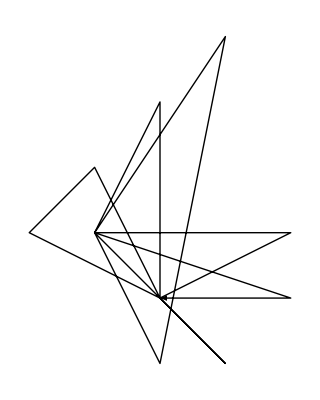
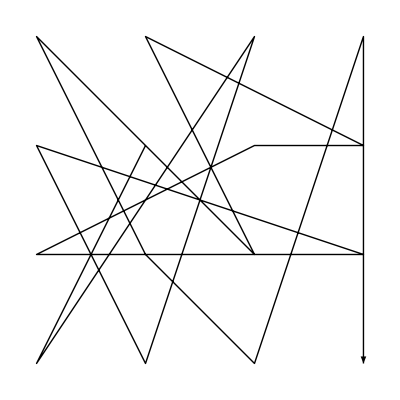
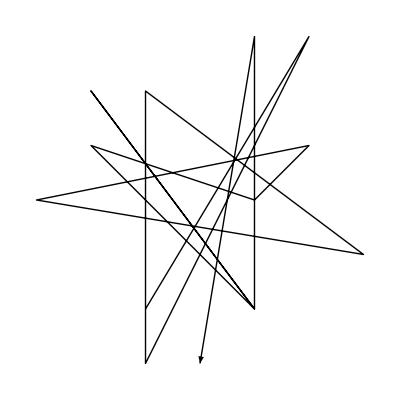
{{(1 | 2 | 3 | 4
5 | 6 | 7 | 8
9 | 10 | 11 | 12
13 | 14 | 15 | 16),{-Graphics-,{{1,0},{1,0},{1,0},{-3,-1},{1,0},{1,0},{1,0},{-3,-1},{1,0},{1,0},{1,0},{-3,-1},{1,0},{1,0},{1,0}},-Graphics-}},{(8 | 1 | 16 | 2
11 | 7 | 14 | 4
15 | 12 | 5 | 9
6 | 13 | 10 | 3),{-Graphics-,{{2,0},{0,-3},{0,2},{-1,-1},{-2,-1},{1,2},{-1,1},{3,-2},{-1,-1},{-2,2},{1,-1},{0,-1},{1,2},{-2,-1},{2,2}},-Graphics-}},{(4 | 8 | 3 | 1
5 | 14 | 13 | 2
10 | 9 | 11 | 15
7 | 6 | 12 | 16),{-Graphics-,{{0,-1},{-1,1},{-2,0},{0,-1},{1,-2},{-1,0},{1,3},{0,-2},{-1,0},{2,0},{0,-1},{0,2},{-1,0},{2,-1},{0,-1}},-Graphics-}},{(12 | 10 | 3 | 15
5 | 1 | 8 | 9
7 | 13 | 11 | 6
2 | 4 | 14 | 16),{-Graphics-,{{-1,-2},{2,3},{-1,-3},{-1,2},{3,-1},{-3,0},{2,1},{1,0},{-2,1},{1,-2},{-2,2},{1,-2},{1,-1},{1,3},{0,-3}},-Graphics-}},{(10 | 15 | 16 | 9
11 | 2 | 1 | 12
6 | 14 | 5 | 13
4 | 8 | 7 | 3),{-Graphics-,{{-1,0},{2,-2},{-3,0},{2,1},{-2,0},{2,-1},{-1,0},{2,3},{-3,0},{0,-1},{3,0},{0,-1},{-2,0},{0,2},{1,0}},-Graphics-}},{(2 | 4 | 16 | 8
11 | 13 | 6 | 1
12 | 15 | 5 | 10
14 | 7 | 9 | 3),{-Graphics-,{{-3,1},{3,-3},{-2,3},{1,-2},{0,1},{-1,-2},{2,3},{-1,-3},{1,1},{-3,1},{0,-1},{1,1},{-1,-2},{1,1},{1,2}},-Graphics-}},{(13 | 14 | 16 | 7
11 | 10 | 12 | 6
1 | 4 | 5 | 2
15 | 9 | 8 | 3),{-Graphics-,{{3,0},{0,-1},{-2,1},{1,0},{1,1},{0,1},{-1,-3},{-1,0},{0,2},{-1,0},{2,0},{-2,1},{1,0},{-1,-3},{2,3}},-Graphics-}},{(7 | 6 | 16 | 13
11 | 9 | 15 | 14
4 | 1 | 5 | 8
12 | 10 | 2 | 3),{-Graphics-,{{1,-1},{1,0},{-3,1},{2,0},{-1,2},{-1,0},{3,-2},{-2,1},{0,-2},{-1,2},{0,-2},{3,3},{0,-1},{-1,0},{0,1}},-Graphics-}},{(6 | 13 | 3 | 14
5 | 12 | 9 | 7
8 | 2 | 11 | 1
10 | 15 | 4 | 16),{-Graphics-,{{-2,0},{1,2},{0,-3},{-2,2},{0,1},{3,-1},{-3,-1},{2,1},{-2,-2},{2,1},{-1,1},{0,1},{2,0},{-2,-3},{2,0}},-Graphics-}},{(9 | 12 | 16 | 10
11 | 8 | 4 | 15
14 | 6 | 5 | 7
1 | 2 | 13 | 3),{-Graphics-,{{1,0},{2,0},{-1,2},{0,-1},{-1,0},{2,0},{-2,1},{-1,1},{3,0},{-3,-1},{1,1},{1,-3},{-2,1},{3,1},{-1,1}},-Graphics-}},{(15 | 9 | 3 | 12
5 | 4 | 2 | 10
13 | 7 | 11 | 14
8 | 1 | 6 | 16),{-Graphics-,{{1,2},{0,1},{-1,-1},{-1,0},{2,-2},{-1,1},{-1,-1},{1,3},{2,-1},{-1,-1},{1,2},{-3,-2},{3,0},{-3,2},{3,-3}},-Graphics-}},{(14 | 7 | 3 | 6
5 | 15 | 10 | 13
2 | 8 | 11 | 4
9 | 12 | 1 | 16),{-Graphics-,{{-2,1},{2,2},{1,-2},{-3,1},{3,1},{-2,0},{0,-2},{-1,-1},{2,2},{0,-1},{-1,-1},{2,2},{-3,1},{1,-1},{2,-2}},-Graphics-}}}

```mathematica
Map[GM,{({{1, 2, 3, 4}, {5, 6, 7, 8}, {9, 10, 11, 12}, {13, 14, 15, 16}}),({{8, 1, 16, 2}, {11, 7, 14, 4}, {15, 12, 5, 9}, {6, 13, 10, 3}}),({{4, 8, 3, 1}, {5, 14, 13, 2}, {10, 9, 11, 15}, {7, 6, 12, 16}}),({{12, 10, 3, 15}, {5, 1, 8, 9}, {7, 13, 11, 6}, {2, 4, 14, 16}}),({{10, 15, 16, 9}, {11, 2, 1, 12}, {6, 14, 5, 13}, {4, 8, 7, 3}}),({{2, 4, 16, 8}, {11, 13, 6, 1}, {12, 15, 5, 10}, {14, 7, 9, 3}}),({{13, 14, 16, 7}, {11, 10, 12, 6}, {1, 4, 5, 2}, {15, 9, 8, 3}}),({{7, 6, 16, 13}, {11, 9, 15, 14}, {4, 1, 5, 8}, {12, 10, 2, 3}}),({{6, 13, 3, 14}, {5, 12, 9, 7}, {8, 2, 11, 1}, {10, 15, 4, 16}}),({{9, 12, 16, 10}, {11, 8, 4, 15}, {14, 6, 5, 7}, {1, 2, 13, 3}}),({{15, 9, 3, 12}, {5, 4, 2, 10}, {13, 7, 11, 14}, {8, 1, 6, 16}}),({{14, 7, 3, 6}, {5, 15, 10, 13}, {2, 8, 11, 4}, {9, 12, 1, 16}})}]
```

```mathematica
{0,-1499,1409,-12032,-2504,15618,1,328,-2011,-9280,3438,2257}
```

```mathematica
Table[{k,Factor[Out[444][[k]]]},{k,801,1000}]//Column
```

```mathematica
Factor[Out[444][[183]]]
```

(-1+y) (-1-261 y-25 y^2+y^3)

```mathematica
183,272,430,707,
```

```mathematica
PermutationOrder[klbj]
```

66

Cycles[{{1,5,16,7,4,3,12,15,11},{2,14,10,8,9,13,6}}]

63

{0,-2566,3394,-1328,-4220,-2487,-540,1470,-6432,5376,9356,-296,3740,18972,-1160,16320,3490,-3753,2804,5078,2888,-8064,-9848,-4740,6205,-2964,-276,15832,1618,8876,-11260,14725,-5555,4748,12425,-16248,8874,-6450,9608,6888,3115,13787,-10764,-1574,-18968,-1164,981,-2653,-5744,-2884,2124,-1648,2517,7735,-1164,-497,-1212,4964,3710,-4404,968,-1495,-10080}

{}

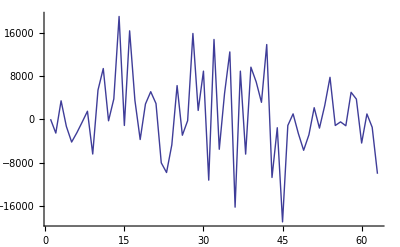

796.032

```mathematica
klbj=RandomPermutation[16]
PermutationOrder[klbj]
odjd=Map[Det[Partition[Permute[Range[16],#],4]]&,GroupElements[PermutationGroup[{klbj}]]]
Select[%,Abs[#]==1&]
ListPlot[odjd,Joined->True]
Mean[odjd]//N
```

```mathematica
a={0,Cycles[{}]};
Monitor[Do[a=Block[{per=RandomPermutation[16]},Piecewise[{{a, PermutationOrder[per]≤First[a]}, {{PermutationOrder[per],per}, PermutationOrder[per]>First[a]}}]],{i,1000000}],{i,a}]
```

```mathematica
a
```

```mathematica
{140,Cycles[{{1,2,10,15,3,5,12},{4,9,7,16,13},{6,11,8,14}}]}
```

```mathematica
{140,Cycles[{{1,6,7,13,10},{2,8,14,11,16,15,4},{3,9,12,5}}]}
```

```mathematica
{140,Cycles[{{1,2,10,13,9},{3,15,6,12,7,4,16},{5,11,14,8}}]}
```

```mathematica
{140,Cycles[{{1,15,12,10},{2,9,14,8,6},{3,11,16,5,4,7,13}}]}
```

```mathematica
{140,{5,1,15,6,7,13,14,16,10,3,2,11,8,12,9,4}}
```

```mathematica
{140,{15,8,16,3,7,1,6,5,12,13,9,14,4,11,2,10}}
```

```mathematica
{140,{14,3,12,5,6,16,10,7,15,9,13,1,2,11,8,4}}
```

```mathematica
{140,{8,3,16,13,14,9,6,5,1,12,4,11,10,7,2,15}}
```